## This is a numerical solver for the Lane Emden equation using Explicit Runge Kutta.

```mathematica
LaneEmden=1/ξ^2 D[(ξ^2 D[θ[ξ], ξ]), ξ]+θ[ξ]^n==0;

sols=NDSolve[{LaneEmden/.n->5/3,θ[0.01]==1,θ'[0.01]==0},θ,{ξ,0.01,10}, MaxSteps->100000, Method->"ExplicitRungeKutta"]
```

{{θ→InterpolatingFunction[{{0.01,10.}},<>]}}

InterpolatingFunction::dmval: Input value {0.000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

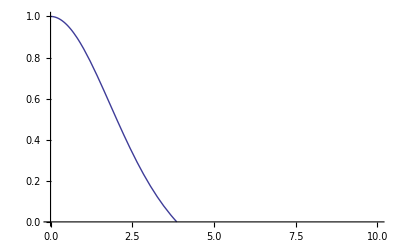

```mathematica
Plot[θ[ξ]/.sols,{ξ,0,10}]
```

```mathematica
vals=θ/.First[sols]
```

InterpolatingFunction[{{0.01,10.}},<>]

```mathematica
data=Table[{i,vals[i]},{i,0.01,4,0.01}];
```

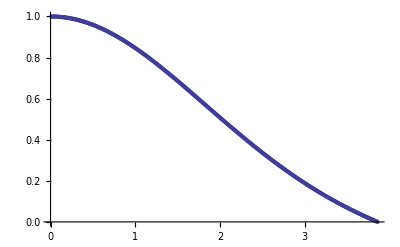

```mathematica
ListPlot[data]
```

```mathematica
data;
```

```mathematica
Select[data, #>0&]
```

{}

```mathematica
data[[1]]
```

{0.01,1.}

```mathematica
x = Table[data[[i]][[1]],{i,1,Length[data]}];
```

```mathematica
z =Select[Re[Table[data[[i]][[2]],{i,1,Length[data]}]],#>0&]
```

{1.,0.999967,0.999889,0.999775,0.999627,0.999445,0.999229,0.99898,0.998697,0.998381,0.998032,0.99765,0.997235,0.996786,0.996305,0.99579,0.995243,0.994662,0.994049,0.993403,0.992725,0.992014,0.99127,0.990494,0.989685,0.988844,0.987971,0.987066,0.986129,0.98516,0.984158,0.983126,0.982061,0.980965,0.979838,0.978679,0.977489,0.976267,0.975015,0.973732,0.972418,0.971074,0.969699,0.968294,0.966859,0.965393,0.963898,0.962373,0.960818,0.959233,0.95762,0.955977,0.954305,0.952604,0.950875,0.949117,0.94733,0.945516,0.943673,0.941803,0.939905,0.937979,0.936026,0.934046,0.932039,0.930005,0.927945,0.925858,0.923745,0.921606,0.919442,0.917251,0.915035,0.912795,0.910529,0.908238,0.905923,0.903583,0.901219,0.898832,0.89642,0.893985,0.891527,0.889046,0.886541,0.884015,0.881466,0.878894,0.876301,0.873686,0.871049,0.868391,0.865713,0.863013,0.860293,0.857552,0.854792,0.852011,0.849211,0.846391,0.843553,0.840695,0.837819,0.834924,0.832011,0.829081,0.826132,0.823166,0.820183,0.817183,0.814166,0.811133,0.808083,0.805017,0.801936,0.798839,0.795727,0.7926,0.789458,0.786302,0.783131,0.779947,0.776748,0.773536,0.770311,0.767073,0.763822,0.760558,0.757283,0.753995,0.750695,0.747384,0.744062,0.740728,0.737384,0.734029,0.730664,0.727289,0.723903,0.720509,0.717105,0.713692,0.71027,0.706839,0.7034,0.699953,0.696498,0.693035,0.689565,0.686088,0.682604,0.679112,0.675615,0.672111,0.668601,0.665086,0.661565,0.658038,0.654507,0.65097,0.647429,0.643883,0.640334,0.63678,0.633222,0.629661,0.626097,0.622529,0.618959,0.615386,0.61181,0.608232,0.604652,0.60107,0.597487,0.593902,0.590316,0.586729,0.583141,0.579553,0.575964,0.572375,0.568786,0.565197,0.561608,0.55802,0.554433,0.550847,0.547262,0.543678,0.540096,0.536515,0.532936,0.529359,0.525785,0.522213,0.518643,0.515076,0.511512,0.507952,0.504394,0.50084,0.497289,0.493743,0.4902,0.486661,0.483126,0.479596,0.47607,0.472549,0.469033,0.465522,0.462016,0.458515,0.45502,0.45153,0.448046,0.444568,0.441096,0.43763,0.43417,0.430717,0.42727,0.423829,0.420396,0.416969,0.41355,0.410137,0.406732,0.403334,0.399944,0.396562,0.393187,0.389819,0.38646,0.383109,0.379766,0.376431,0.373105,0.369787,0.366478,0.363177,0.359885,0.356602,0.353328,0.350063,0.346807,0.34356,0.340323,0.337095,0.333876,0.330667,0.327468,0.324278,0.321098,0.317928,0.314767,0.311617,0.308477,0.305347,0.302227,0.299117,0.296018,0.292929,0.289851,0.286783,0.283725,0.280678,0.277642,0.274617,0.271602,0.268598,0.265605,0.262623,0.259652,0.256692,0.253743,0.250805,0.247878,0.244963,0.242058,0.239165,0.236283,0.233412,0.230553,0.227705,0.224868,0.222043,0.219229,0.216427,0.213636,0.210857,0.208089,0.205332,0.202588,0.199855,0.197133,0.194423,0.191725,0.189038,0.186363,0.1837,0.181048,0.178408,0.17578,0.173163,0.170558,0.167965,0.165383,0.162813,0.160255,0.157709,0.155174,0.152651,0.150139,0.147639,0.145151,0.142675,0.14021,0.137756,0.135315,0.132885,0.130466,0.12806,0.125664,0.123281,0.120908,0.118548,0.116199,0.113861,0.111535,0.10922,0.106916,0.104624,0.102344,0.100075,0.0978166,0.0955699,0.0933345,0.0911103,0.0888974,0.0866956,0.0845049,0.0823254,0.080157,0.0779996,0.0758532,0.0737178,0.0715933,0.0694797,0.0673771,0.0652852,0.0632042,0.0611339,0.0590743,0.0570254,0.0549871,0.0529595,0.0509423,0.0489357,0.0469396,0.0449538,0.0429785,0.0410135,0.0390587,0.0371142,0.0351799,0.0332557,0.0313416,0.0294375,0.0275434,0.0256593,0.023785,0.0219206,0.0200659,0.0182209,0.0163856,0.0145599,0.0127438,0.0109371,0.00913992,0.00735207,0.00557352,0.00380422,0.00204411,0.000293103}

```mathematica
datareal = Table[{x[[i]],z[[i]]},{i,1,Length[z]}];
```

```mathematica
ListPlot[datareal]
```

-Graphics-

```mathematica
Export[ "/Users/kaitlin/TALENT/project1/sedov-solution/laneEmbden.dat",datareal,"Table"]
```

/Users/kaitlin/TALENT/project1/sedov-solution/laneEmbden.dat